```mathematica
plot1=Rasterize[Plot[{Sin[x],2*Sin[2*x-Pi]},{x,0,6Pi},Frame->True,FrameLabel->{"x [rad]","f(x)"},LabelStyle->Directive[{FontSize->12},Black],PlotStyle->{{Blue},{Dashed}},GridLines->{{0,Pi, 2Pi,3Pi,4Pi,5Pi},{-3,-2,-1,0,1,2,3}},FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{0,Pi,2Pi,3Pi,4Pi,5Pi,6Pi},None}},PlotLegends->"Expressions"]]
```

-Graphics-

```mathematica
plot2=Rasterize[Plot[3*Cos[x],{x,0,6Pi},Frame->True,FrameLabel->{"x [rad]","f(x)"},LabelStyle->Directive[{FontSize->12},Black],PlotStyle->{{Blue},{Dashed}},GridLines->{{0,Pi, 2Pi,3Pi,4Pi,5Pi},{-3,-2,-1,0,1,2,3}},FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{0,Pi,2Pi,3Pi,4Pi,5Pi,6Pi},None}},PlotLegends->{"3cos(x)"}]]
```

-Graphics-

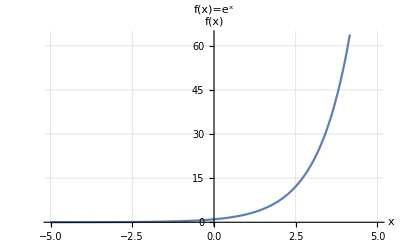

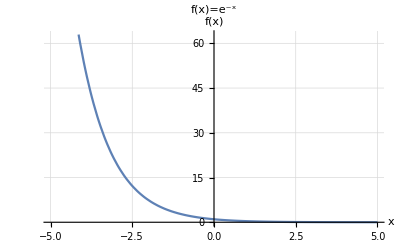

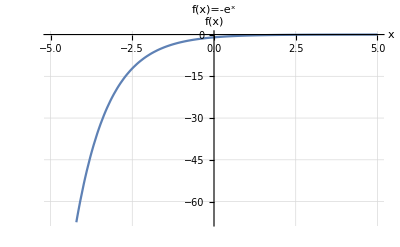

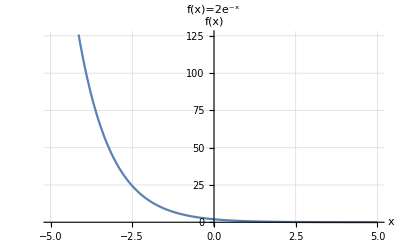

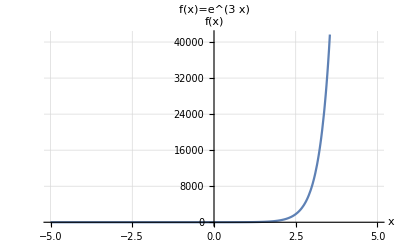

```mathematica
plot3=Plot[{Exp[x]},{x,-5,5},AxesLabel->{"x","f(x)"},PlotLabel->Style[Framed["f(x)=e^x"],14],LabelStyle->Directive[{FontSize->12},Black],GridLines->Automatic]
plot4=Plot[{Exp[-x]},{x,-5,5},AxesLabel->{"x","f(x)"},PlotLabel->Style[Framed["f(x)=e^-x"],14],LabelStyle->Directive[{FontSize->12},Black],GridLines->Automatic]
plot5=Plot[{-Exp[-x]},{x,-5,5},AxesLabel->{"x","f(x)"},PlotLabel->Style[Framed["f(x)=-e^x"],14],LabelStyle->Directive[{FontSize->12},Black],GridLines->Automatic]
plot6=Plot[{2Exp[-x]},{x,-5,5},AxesLabel->{"x","f(x)"},PlotLabel->Style[Framed["f(x)=2e^-x"],14],LabelStyle->Directive[{FontSize->12},Black],GridLines->Automatic]
plot7=Plot[{Exp[3x]},{x,-5,5},AxesLabel->{"x","f(x)"},PlotLabel->Style[Framed["f(x)=e^(3  x)"],14],LabelStyle->Directive[{FontSize->12},Black],GridLines->Automatic]
```

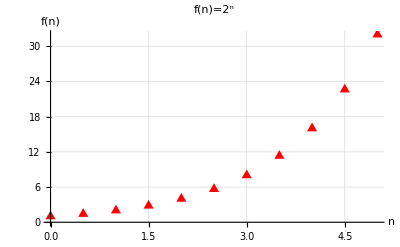

```mathematica
plot8=ListPlot[Table[{x,2^x},{x,0,5,0.5}],GridLines->Automatic,AxesLabel->{"n","f(n)"},PlotLabel->Style[Framed["f(n)=2^n"],14],LabelStyle->Directive[{FontSize->12},Black],PlotMarkers->{▲,12},PlotStyle->Red]
```

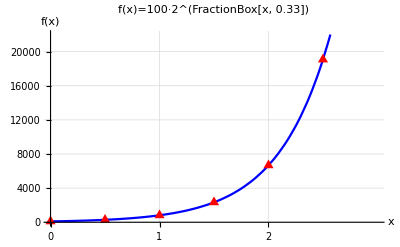

```mathematica
plot9=Plot[{100*2^(x/0.33)},{x,0,5},PlotRange->{{0,3},{0,22000}},GridLines->Automatic,AxesLabel->{"x","f(x)"},PlotLabel->Style[Framed["f(x)=100·2^(FractionBox[x,  0.33])"],14],LabelStyle->Directive[{FontSize->12},Black],PlotStyle->Blue,Ticks->{{0,0.5,1,1.5,2,2.5},Automatic}];
plot10=ListPlot[Table[{x,100*2^(x/0.33)},{x,0,5,0.5}],PlotMarkers->{▲,12},PlotStyle->Red];
Show[plot9,plot10]
```

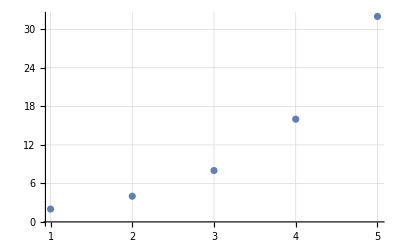

```mathematica
ListPlot[Table[{x,2^x},{x,5}],GridLines->Automatic]
```

```mathematica
Trick:
(*PlotLabel->Style[Framed[f(x)=100·2^HoldForm[x/0.33]],16,Black,Background->Lighter[Yellow]]*)
```